藤井陽一，『光・量子エレクトロニクス』

```mathematica
(*========================= 初期化セル =========================*)
(*屈折率の関数を定義したノートブックを呼び出して評価*)
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
RefractiveIndexDefNotebookNames={
"Gehrsitz(2000)に基づくAlGaAsの組成比・温度・波長に依存した屈折率の導出.nb",(*nAlGaAs[(*Al組成比x*),(*温度T*),(*波長λ*)]*)
"SiO2とTiO2の室温の屈折率の導出.nb"};(*nSiO2RoomT[(*波長λ*)],nTiO2RoomT[(*波長λ*)]*)
Do[
nb=NotebookOpen[FileNameJoin[{NotebookDirectory[],RefractiveIndexDefNotebookName}]];
NotebookEvaluate[nb,EvaluationElements->"InitializationCell"];
NotebookClose[nb]
,{RefractiveIndexDefNotebookName,RefractiveIndexDefNotebookNames}]
(*Plot画像保存用関数*)
ExpVectorImg[plot_,name_]:=Export[FileNameJoin[{NotebookDirectory[],name<>".svg"}],plot,"SVG"]
```

```mathematica
r[n1_,n2_,λ0_]:=Sqrt[(n1^2-n2^2)*(2π/λ0)^2]
TargetWL=0.81;
n1=2.1810;(*AlN*)
n2=nSiO2RoomT[(*波長λ*)TargetWL]
d=((2/2)*(TargetWL/n1))/2
```

1.45315

0.185695

```mathematica
rd2=(r[n1,n2,TargetWL]*d)^2
```

5.48826

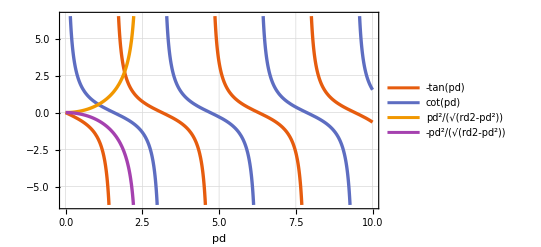

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\単層スラブ導波路_fig1.svg

```mathematica
Plot1=Plot[{
(*遇パリティ*)-Tan[pd],
(*奇パリティ*)Cot[pd],
(*伝送モード*)(pd^2)/Sqrt[(rd2)-(pd^2)],
(*放射モード*)-(pd^2)/Sqrt[(rd2)-(pd^2)]
},{pd,0,10},
FrameLabel->{"pd",""},GridLines->Automatic,PlotStyle->{Thickness[0.006]},
ImageSize-> Scaled[0.6],FrameStyle->Directive[FontSize-> Scaled[0.02]],
PlotTheme->{(*"Monochrome",*)"Scientific","SansLabels"},PlotLegends->"Expressions"]
ExpVectorImg[Plot1,"単層スラブ導波路_fig1"]
```

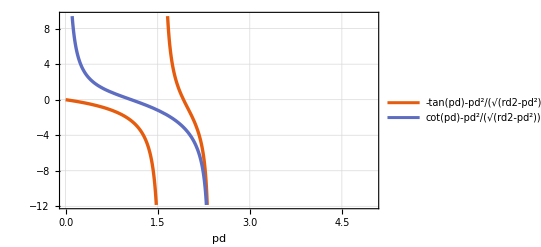

```mathematica
Plot[{
(*遇パリティ*)-Tan[pd]-((pd^2)/Sqrt[(rd2)-(pd^2)]),
(*奇パリティ*)Cot[pd]-((pd^2)/Sqrt[(rd2)-(pd^2)])
},{pd,0,5},
FrameLabel->{"pd",""},GridLines->Automatic,PlotStyle->{Thickness[0.006]},
ImageSize-> Scaled[0.6],FrameStyle->Directive[FontSize-> Scaled[0.02]],
PlotTheme->{(*"Monochrome",*)"Scientific","SansLabels"},PlotLegends->"Expressions"]
```

```mathematica
FindRoot[(*遇パリティ*)-Tan[pd]-((pd^2)/Sqrt[(rd2)-(pd^2)]),{pd,2}]
FindRoot[(*奇パリティ*)Cot[pd]-((pd^2)/Sqrt[(rd2)-(pd^2)]),{pd,1}]
```

{pd→1.92}

{pd→1.06918}

```mathematica
NSolve[(pd/d)^2==n1^2*(2π/TargetWL)^2-k^2,k]/.FindRoot[(*遇パリティ*)-Tan[pd]-((pd^2)/Sqrt[(rd2)-(pd^2)]),{pd,2}]
```

{{k→-13.3908},{k→13.3908}}

```mathematica
NSolve[(pd/d)^2==n1^2*(2π/TargetWL)^2-k^2,k]/.FindRoot[(*奇パリティ*)Cot[pd]-((pd^2)/Sqrt[(rd2)-(pd^2)]),{pd,1}]
```

{{k→-15.9082},{k→15.9082}}

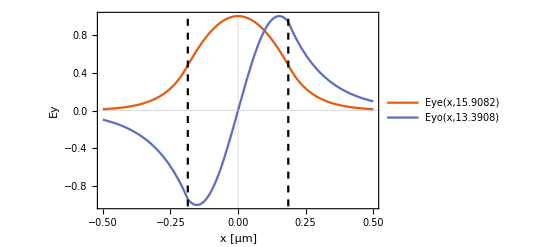

C:\Users\峻之\Dropbox\00 博士研究\Mathematica\光学薄膜計算\単層スラブ導波路_fig2.svg

```mathematica
LinePlot=ListLinePlot[{{{d,-100},{d,100}},{{-d,-100},{-d,100}}},PlotStyle->Directive[Black,Dashed]];
p[k_]:=Sqrt[n1^2*(2π/TargetWL)^2-k^2]
q[k_]:=Sqrt[k^2-n2^2*(2π/TargetWL)^2]
Eye[x_,k_]:=If[Abs[x]≤d,Cos[p[k]*x],0]+If[Abs[x]>d,Cos[p[k]*d]*Exp[-q[k]*(Abs[x]-d)],0]
Eyo[x_,k_]:=If[Abs[x]≤d,Sin[p[k]*x],0]+If[Abs[x]>d,(x/Abs[x])*Sin[p[k]*d]*Exp[-q[k]*(Abs[x]-d)],0]
plot=Plot[{
Eye[x,15.908150310077186],
Eyo[x,13.390816814102033]}
,{x,-0.5,0.5},PlotRange->Full,FrameLabel->{"x [μm]","Ey"},
PlotTheme->{(*"Monochrome",*)"Scientific","SansLabels"},PlotLegends->"Expressions"];
Plot2=Show[{plot,LinePlot}]
ExpVectorImg[Plot2,"単層スラブ導波路_fig2"]
```